# Block Arnoldi

A block Arnoldi scheme looks very much like the Arnoldi scheme.

## Script

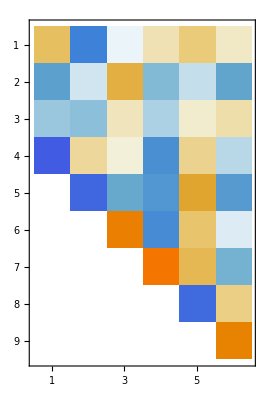

```mathematica
{m,b}={23,3};
A=RandomReal[{-1,1},{m,m}];
Q1= QRDecomposition[RandomReal[{-1,1},{m,b}]]⟦1⟧ᵀ;
AQ1=A.Q1;
H11=(Q1ᵀ.AQ1);
Q2=AQ1-Q1.H11;
{Q2,R21}= QRDecomposition[Q2];Q2=Q2ᵀ;
AQ2=A.Q2;
H12=(Q1ᵀ.AQ2);H22=(Q2ᵀ.AQ2);
Q3=AQ2-Q1.H12-Q2.H22;
{Q3,R32}= QRDecomposition[Q3];Q3=Q3ᵀ;
QQ2=ArrayFlatten[{{Q1,Q2}}];
QQ3=ArrayFlatten[{{Q1,Q2,Q3}}];
HH =ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})];
MatrixPlot[HH]
Norm[A.QQ2-QQ3.HH]
```

## Function and Testing

```mathematica
BlockArnoldiStart[A_][Q1_]:= Module[{AQ1,H11,Q2,R21,AQ2,H12,H22,Q3,R32},
AQ1=A.Q1;
H11=(Q1ᵀ.AQ1);
Q2=AQ1-Q1.H11;
{Q2,R21}= QRDecomposition[Q2];Q2=Q2ᵀ;
AQ2=A.Q2;
H12=(Q1ᵀ.AQ2);H22=(Q2ᵀ.AQ2);
Q3=AQ2-Q1.H12-Q2.H22;
{Q3,R32}= QRDecomposition[Q3];Q3=Q3ᵀ;
{ArrayFlatten[{{Q1,Q2,Q3}}],ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})]}
]
```

Testing

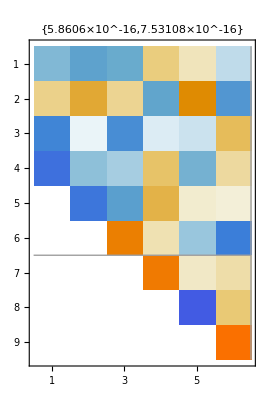

```mathematica
{m,b}={22,3};
A=RandomReal[{-1,1},{m,m}];
QIn=QRDecomposition[RandomReal[{-1,1},{m,b}]]⟦1⟧ᵀ;
{QOut,HOut}=BlockArnoldiStart[A][QIn];
MatrixPlot[HOut,
Mesh->{{2b},{2b}},
PlotLabel->Map[Norm,{QOutᵀ.QOut-IdentityMatrix[3b],A.QOut⟦All,1;;2b⟧-QOut.HOut}]]
```